# Лабораторная работа 2.4 Компьютерная сцинтилляционная γ - спектроскопия

## Нехаев Александр, 654гр.

## Введение

Цель работы : определить зависимость энергии и интенсивности гамма-линий от различных гамма источников и идентифицировать их.

В работе используются : сцинтиллятор, ФЭУ, предусилитель импульсов, высоковольтный блок питания для ФЭУ, АЦП, компьютер.

### Теоретическое введение

Фотоэффект. Это процесс взаимодействия гамма - кванта с электроном, связанным с атомом, при котором электрону передается вся энергия гамма - кванта.При этом электрону сообщается кинетическая энергия T_e=E_γ-I_i, где E_γ– энергия гамма - кванта, I_i-- потенциал ионизации i - той оболочки атома.Фотоэффект особенно существенен для тяжелых веществ, где он идет с заметной вероятностью даже при высоких энергиях гамма - квантов.В легких веществах фотоэффект становится заметен лишь при относительно небольших энергиях гамма - квантов.Наряду с фотоэффектом, при котором вся энергия гамма - кванта передается атомному электрону, взаимодействие гамма - излучения со средой может приводить к его рассеянию, т.е.отклонению от первоначального направления распространения на некоторый угол.

Эффект Комптона. Это упругое рассеяние фотона на свободном электроне, сопровождающееся изменением длины волны фотона (реально этот процесс происходит на слабо связанных с атомом внешних электронах).Максимальная энергия образующихся комптоновских электронов соответствует рассеянию гамма - квантов на 180° и равна

E_max=(η ω)/(1+(m c^2)/(η ω))

Процесс образования электрон - позитронных пар. При достаточно высокой энергии гамма - кванта наряду с фотоэффектом и эффектом Комптона может происходить третий вид взаимодействия гамма - квантов с веществом-- образование электрон - позитронных пар. Процесс образования пар не может происходить в пустоте, так как в этом случае не выполняются законы сохранения энергии и импульса.В присутствии ядра или электрона процесс образования пары гамма - квантом возможен, так как можно распределить энергию и импульс гамма - кванта между тремя частицами без противоречия с законами сохранения.При этом если процесс образования пары идет в кулоновском поле ядра или протона, то энергия образующегося ядра отдачи оказывается весьма малой,так что пороговая энергия гамма-кванта E_0,необходимая для образования пары,практически совпадает с удвоенной энергией покоя электрона E_0≅ 2m c^2=1.022 МэВ.

Появивишийся в результате процесса образования пар электрон свою энергию на ионизацию среды.Таким образом, вся энергия электрона остается в детекторе.Позитрон будет двигаться до тех пор, пока практически не остановится, а затем аннигилирует с электроном среды, в результате чего появятся два гамма - кванта.Т.е., кинетическая энергия позитрона также останется в детекторе.Далее возможны три варианта развития событий :

оба родившихся гамма - кванта не вылетают из детектора, и тогда вся энергия первичного гамма - кванта останется в детекторе, а в спектре появится пик с E=E_γ;

один из родившихся гамма-квантов покидает детектор, и в спектре появляется пик, соответствующий энергии E=E_γ-E_0, где E_0=m c^2=511 кэВ;

оба родившихся гамма-кванта покидают детектор, и в спектре появляется пик, соотвествующий энергии E=E_γ-2 E_0, где 2 E_0=2m c^2=1022 кэВ.

Таким образом, любой спектр, получаемый с помощью гамма - спектрометра, описывается несколькими компонентами, каждая из которых связана с определенным физическим процессом.Как описано выше, основными физическими процессами взаимодействия гамма - квантов с веществом является фотоэффект, эффект Компотона и образование электрон - позитронных пар, и каждый из них вносит свой вклад в образование спектра. Помимо этих процессов, добавляется экспонента, связанная с наличием фона, пик характеристического излучения, возникающий при взаимодействии гамма - квантов с окружающим веществом, а также пик обратного рассеяния, образующийся при энергии квантов E_γ>> m c^2/2 в результате рассеяния гамма-квантов на большие углы на материалах  конструктивных элементов детектора и защиты. Положение пика обратного рассеяния определяется по формуле:

E_обр=E/(1+2E/m c^2)

где E – энергия фотопика.

Энергетическое разрешение спектрометра. Даже при поглощении частиц с одинаковой энергией амплитуда импульса на выходе фотоприёмника сцинтилляционного детектора меняется от события к событию. Это связано:

со статистическим характером процессов сбора фотонов на фотоприёмнике и последующего усиления,

с различной вероятностью доставки фотона к фотоприемнику из разных точек сцинтиллятора,

с разбросом высвечиваемого числа фотонов

В результате в набранном спектре линия (которая для идеального детектора представляла бы дельта - функцию) оказывается размытой, её часто описывают гауссианом.

Энергетическим разрешением спектрометра называется величина

R_i=(Δ E_i)/E_i

где Δ E_i– ширина пика полного поглощения, измеренная на половине высоты, E_i– энергия регистрируемого γ - излучения. Значение E_iпропорционально среднему числу фотонов OverBar[n_i] на выходе ФЭУ, т.е. :

E_i=α OverBar[n_i]

Полуширина пика полного поглощения Δ E_i пропорциональна среднеквадратичной флуктуации Δ OverBar[n_i]. Т.к. OverBar[n_i] является дискретной случайной величиной, которая распределена по закону Пуассона, то OverBar[Δ n_i]=√OverBar[n_i]и поэтому

ΔE_i=αOverBar[Δ n_i]=α√OverBar[n_i]

Из (4) и (5) получаем, что

R_i=(Δ E_i)/E_i=const/(√E_i)

Поскольку энергетическое разрешение зависит от энергии, его следует указывать для конкретной энергии.Чаще всего разрешение указывают для энергии гамма - линии ^137 Cs (661.7 кэВ).

## Ход работы

Используем спектр ^22 Na как калибровочный график :

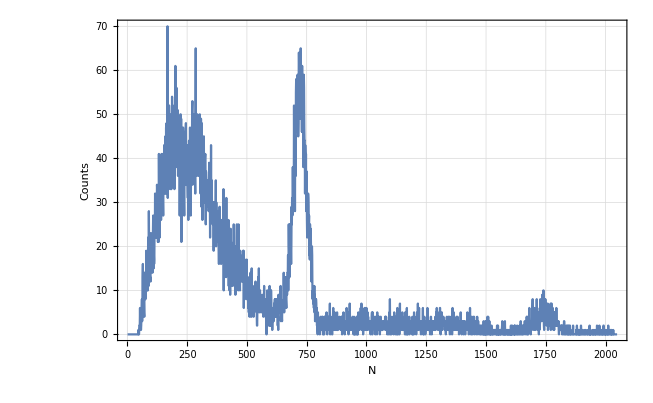

```mathematica
Calibration=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/calibration.xlsx"][[1]][[7;;All]];
Show[ListLinePlot[Calibration, PlotTheme->"Detailed"],FrameLabel->{{HoldForm[Counts],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Построим калибровочный график зависимости номера канала N от энергии γ - кванта E_i.Предварительно аппроксимируем пики по функции Гаусса :

y(x)=A ⅇ^(-(x-x0)^2/(2 sigma^2))+B x+C

Таким образом, спектр с аппроксимированными пиками имеет следующий вид :

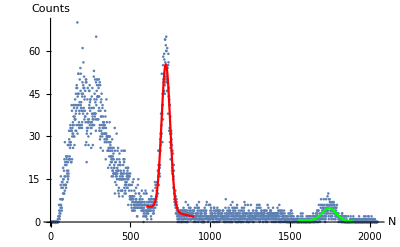

```mathematica
GaussianFit[leftBorder_,rightBorder_,data_]:=
FindFit[data,{a*Exp[-(x-x0)^2/(2*sigma^2)]+b*x+c,{leftBorder≤ x0≤ rightBorder}},{a, x0, sigma, b, c},x];
leftBorder = 600;
rightBorder = 900;
leftBorder2 = 1550;
rightBorder2 = 1900;
Peak511Calibration=Calibration[[leftBorder;;rightBorder]];
Peak1275Calibration=Calibration[[leftBorder2;;rightBorder2]];
GaussianModel[x_]=a*Exp[-(x-x0)^2/(2*sigma^2)]+b*x+c;
fit=FindFit[Peak511Calibration,{GaussianModel[x],{leftBorder≤ x0≤ rightBorder}},{a, x0, sigma, b, c},x];
fit2=FindFit[Peak1275Calibration,{GaussianModel[x],{leftBorder2≤ x0≤ rightBorder2}},{a, x0, sigma, b, c},x];
Show[ListPlot[Calibration],Plot[GaussianModel[x]/.fit,{x,leftBorder,rightBorder},PlotStyle->Red],Plot[GaussianModel[x]/.fit2,{x,leftBorder2,rightBorder2},PlotStyle->Green],AxesLabel->{HoldForm[N],HoldForm[Counts]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotTheme->"Detailed"]
```

Координаты пиков по горизонтальной оси соответсвтуют параметру x_0. Для данных пиков:

```mathematica
Subscript[x, 01]:
```

```mathematica
x0/.fit
```

722.438

```mathematica
Subscript[x, 02]:
```

```mathematica
x0/.fit2
```

1746.

Тогда калибровочный график имеет вид :

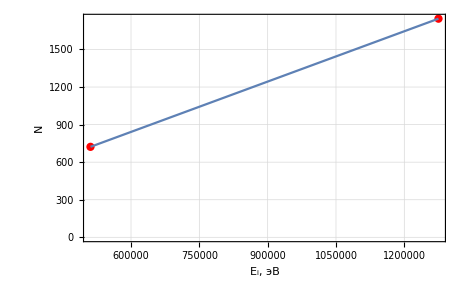

```mathematica
Calibrator=({{511*1000, 722.438}, {1275*1000, 1745.9955}});
calibFit=LinearModelFit[Calibrator,x,x];
calibFitFunc[x_]:=calibFit["BestFit"];
Show[ListPlot[Calibrator,PlotStyle->Red,PlotTheme->"Detailed"],Plot[calibFitFunc[x],{x,511000,1275000}],FrameLabel->{{HoldForm[N],None},{RawBoxes[RowBox[{SubscriptBox["E","i"],","," ","эВ"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Функция для перевода номера канала в энергию имеет вид :

```mathematica
TraditionalForm[Reduce[calibFitFunc[x]=="N_i",x]]/.x-> "E_i"
```

E_i==746.416 N_i-28239.5

Используя калибровочный график, определим для всех остальных источников значения энергии пиков полного поглощения E_i, их ширины на половине высоты Δ H_i и энергетическое разрешение R_i.

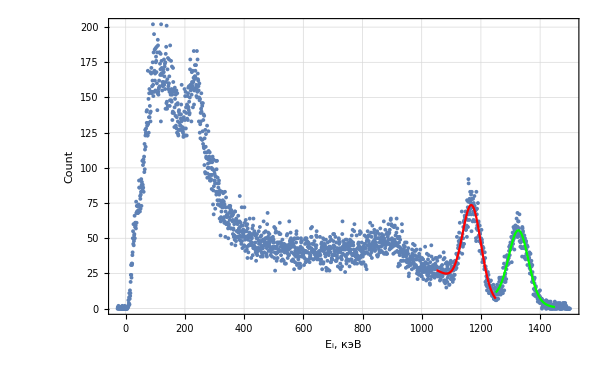

```mathematica
Cobalt60S=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/Co60.xlsx"][[1]][[7;;All]];
Cobalt60=Cobalt60S;
For[i=1,i≤Length[Cobalt60],i++,
Cobalt60[[i,1]]=Calibrate[Cobalt60[[i,1]]]/1000;
]
fitPeak1Co=FindFit[Cobalt60[[1400;;1700]],{GaussianModel[x],{1050≤ x0≤ 1250}},{a, x0, sigma, b, c},x];
fitPeak2Co=FindFit[Cobalt60[[1690;;2000]],{GaussianModel[x],{1250≤ x0≤ 1450}},
{a,x0,sigma,b,c},x];
Show[ListPlot[Cobalt60,Frame->True,FrameLabel->{{"Count" ,None},{"E_i, кэВ","^60Co"}},PlotTheme->"Detailed"],Plot[GaussianModel[x]/.fitPeak1Co,{x,1050,1250},PlotStyle->Red],
Plot[GaussianModel[x]/.fitPeak2Co,{x,1250,1450},PlotStyle->Green]
]
```

```mathematica
fitPeak1Co
fitPeak2Co
```

{a→59.2693,x0→1169.01,sigma→-30.7411,b→-0.110614,c→143.527}

{a→50.2842,x0→1327.06,sigma→-33.2253,b→-0.0351206,c→51.9475}

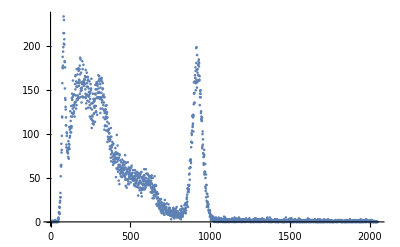

```mathematica
Cesium137S=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/Cs137.xlsx"][[1]][[7;;All]];
Cesium137=Cesium137S;
ListPlot[Cesium137]
For[i=1,i≤Length[Cesium137],i++,
Cesium137[[i,1]]=Calibrate[Cesium137[[i,1]]]/1000;
]
```

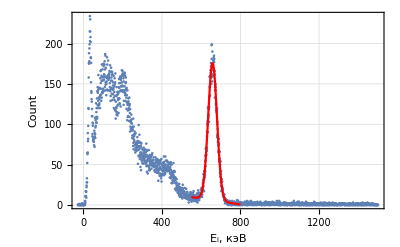

{a→169.868,x0→658.017,sigma→22.4864,b→-0.0365818,c→29.8604}

```mathematica
fitPeak1Cs=FindFit[Cesium137[[800;;1100]],{GaussianModel[x],{550≤ x0≤ 800}},{a, x0, sigma, b, c},x];
Show[ListPlot[Cesium137,Frame->True,FrameLabel->{"E_i, кэВ","Count" },PlotTheme->"Detailed"],Plot[GaussianModel[x]/.fitPeak1Cs,{x,550,800},PlotStyle->Red]
]
fitPeak1Cs
```

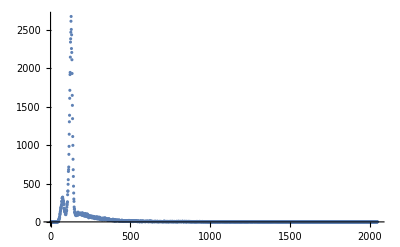

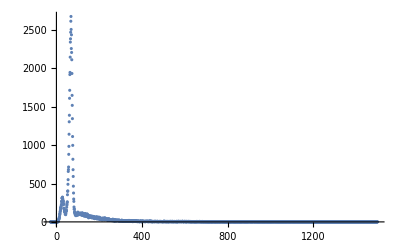

```mathematica
Am241S=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/Am241.xlsx"][[1]][[7;;All]];
Am241=Am241S;
ListPlot[Am241,PlotRange->All]
For[i=1,i≤Length[Am241],i++,
Am241[[i,1]]=Calibrate[Am241[[i,1]]]/1000;
]
ListPlot[Am241,PlotRange->All]
```

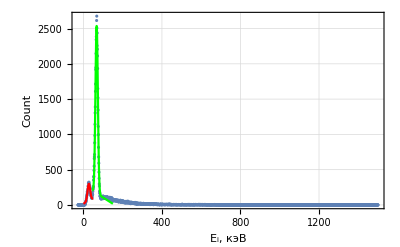

{a→240.611,x0→27.739,sigma→6.72514,b→1.49067,c→16.8314}

{a→2372.8,x0→67.4993,sigma→6.14005,b→-1.77949,c→283.629}

```mathematica
fitPeak1Am=FindFit[Am241[[1;;100]],{GaussianModel[x],{1≤ x0≤ 50}},{a, x0, sigma, b, c},x];
fitPeak2Am=FindFit[Am241[[100;;200]],{GaussianModel[x],{45≤ x0≤ 150}},{a, x0, sigma, b, c},x];
Show[ListPlot[Am241,Frame->True,FrameLabel->{"E_i, кэВ","Count" },PlotTheme->"Detailed",PlotRange->All],
Plot[GaussianModel[x]/.fitPeak1Am,{x,0,50},PlotStyle->Red],
Plot[GaussianModel[x]/.fitPeak2Am,{x,45,150},PlotStyle->Green]
]
fitPeak1Am
fitPeak2Am
```

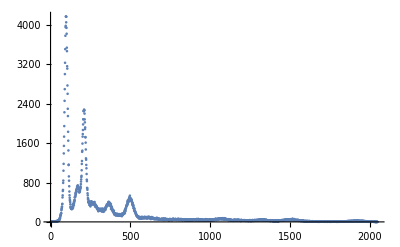

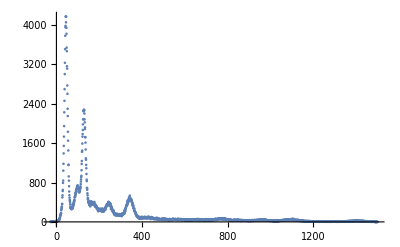

```mathematica
Eu152S=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/Eu152.xlsx"][[1]][[7;;All]];
Eu152=Eu152S;
ListPlot[Eu152,PlotRange->All]
For[i=1,i≤Length[Eu152],i++,
Eu152[[i,1]]=Calibrate[Eu152[[i,1]]]/1000;
]
ListPlot[Eu152,PlotRange->All]
```

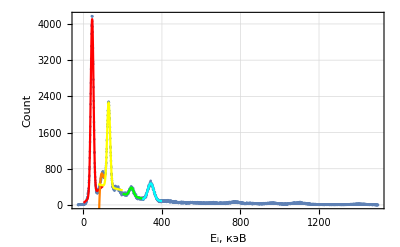

{a→3896.56,x0→44.4872,sigma→-7.02666,b→3.75551,c→41.8683}

{a→9581.95,x0→75.,sigma→23.8433,b→231.153,c→-28006.3}

{a→1864.31,x0→128.477,sigma→-7.78273,b→-1.08671,c→539.736}

{a→183.065,x0→245.012,sigma→10.7026,b→-1.03143,c→451.439}

{a→372.552,x0→343.194,sigma→15.065,b→-0.329873,c→216.548}

```mathematica
fitPeak1Eu=FindFit[Eu152[[10;;150]],{GaussianModel[x],{1≤ x0≤ 100}},{a, x0, sigma, b, c},x];
fitPeak2Eu=FindFit[Eu152[[150;;200]],{GaussianModel[x],{75≤ x0≤ 110}},{a, x0, sigma, b, c},x];
fitPeak3Eu=FindFit[Eu152[[190;;260]],{GaussianModel[x],{110≤ x0≤ 150}},{a, x0, sigma, b, c},x];
fitPeak4Eu=FindFit[Eu152[[290;;460]],{GaussianModel[x],{200≤ x0≤ 300}},{a, x0, sigma, b, c},x];
fitPeak5Eu=FindFit[Eu152[[450;;600]],{GaussianModel[x],{300≤ x0≤ 400}},{a, x0, sigma, b, c},x];
fitPeak6Eu=FindFit[Eu152[[239;;310]],{GaussianModel[x],{150≤ x0≤ 200}},{a, x0, sigma, b, c},x];
Show[ListPlot[Eu152,Frame->True,FrameLabel->{"E_i, кэВ","Count" },PlotTheme->"Detailed",PlotRange->All],
Plot[GaussianModel[x]/.fitPeak1Eu,{x,1,100},PlotStyle->Red],
Plot[GaussianModel[x]/.fitPeak2Eu,{x,75,110},PlotStyle->Orange],
Plot[GaussianModel[x]/.fitPeak3Eu,{x,75,200},PlotStyle->Yellow],
Plot[GaussianModel[x]/.fitPeak4Eu,{x,200,300},PlotStyle->Green],
Plot[GaussianModel[x]/.fitPeak5Eu,{x,300,400},PlotStyle->Cyan]
]
fitPeak1Eu
fitPeak2Eu
fitPeak3Eu
fitPeak4Eu
fitPeak5Eu
```

```mathematica
Uncalibrate[y_]:=0.001339734947643979 (28239.497536777086+1. y);
```

```mathematica
fits={{name-> "Cobalt",fitPeak1Co},{name-> "Cobalt",fitPeak2Co},{name-> "Cesium",fitPeak1Cs},{name-> "Americium",fitPeak1Am},{name-> "Americium",fitPeak2Am},{name->"Europium",fitPeak1Eu},{name->"Europium",fitPeak2Eu},{name->"Europium",fitPeak3Eu},{name->"Europium",fitPeak4Eu},{name->"Europium",fitPeak5Eu}};
```

```mathematica
ResultTable=({{"Source", "N_i", "ΔN_i", "E_i", "ΔE_i", "R_i"}});
For[i=1,i≤ 10,i++,
ResultTable=Append[ResultTable,{name/.fits[[i]][[1]],Uncalibrate[(x0)*1000],Uncalibrate[(2 √(2Log[2])*Abs[sigma])*1000],Quantity[x0,"Kiloelectronvolts"],Quantity[2 √(2Log[2])*Abs[sigma],"Kiloelectronvolts"],Quantity[2 √(2Log[2])*Abs[sigma],"Kiloelectronvolts"]/Quantity[x0,"Kiloelectronvolts"]}/.fits[[i]][[2]]];
]
ResultTable//Grid
```

Source | N_i | ΔN_i | E_i | ΔE_i | R_i
Cobalt | 1604. | 134.817 | 1169.01 keV | 72.3899 keV | 0.061924
Cobalt | 1815.74 | 142.654 | 1327.06 keV | 78.2396 keV | 0.0589571
Cesium | 919.402 | 108.774 | 658.017 keV | 52.9515 keV | 0.0804713
Americium | 74.9963 | 59.0501 | 27.739 keV | 15.8365 keV | 0.570911
Americium | 128.265 | 57.2043 | 67.4993 keV | 14.4587 keV | 0.214205
Europium | 97.4345 | 60.0014 | 44.4872 keV | 16.5465 keV | 0.371939
Europium | 138.314 | 113.055 | 75. keV | 56.1468 keV | 0.748624
Europium | 209.958 | 62.3867 | 128.477 keV | 18.3269 keV | 0.142648
Europium | 366.084 | 71.5985 | 245.012 keV | 25.2028 keV | 0.102864
Europium | 497.623 | 85.3612 | 343.194 keV | 35.4755 keV | 0.103368

```mathematica
Test6thEquTable=Transpose[Append[{1/ResultTable[[2;;All,4]]},ResultTable[[2;;All,6]]]^2];
Test6thEquTable=Delete[Test6thEquTable,{7}]
```

{{7.31748×10^-7 /keV^2,0.00383458},{5.67832×10^-7 /keV^2,0.00347594},{2.30954×10^-6 /keV^2,0.00647563},{0.00129963 /keV^2,0.32594},{0.000219483 /keV^2,0.0458839},{0.000505278 /keV^2,0.138339},{0.0000605831 /keV^2,0.0203485},{0.0000166582 /keV^2,0.010581},{8.49024×10^-6 /keV^2,0.010685}}

```mathematica
Test6thEquApprox=LinearModelFit[QuantityMagnitude[Test6thEquTable],x,x]
```

FittedModel[0.00455847+248.157 x]

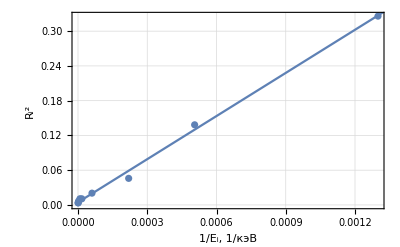

```mathematica
Show[ListPlot[Test6thEquTable,PlotTheme->"Detailed",Frame->True,FrameLabel->{"1/E_i, 1/кэВ","R_i^2" }],Plot[Test6thEquApprox["BestFit"],{x,0,10}] ]
```

```mathematica
ComptonEdge[photonEnergy_]:=UnitConvert[(2 photonEnergy^2)/(Quantity[1,"ElectronMass"]*Quantity[1,"SpeedOfLight"]^2+2*photonEnergy),"Kiloelectronvolts"];
```

```mathematica
Edges=({{"Cobalt", ComptonEdge[Quantity[1.173,"Megaelectronvolts"]], 915.2}, {"Cesium", ComptonEdge[Quantity[661.7,"Kiloelectronvolts"]], 435.9}, {"Na", ComptonEdge[Quantity[1.275,"Megaelectronvolts"]], 1017.1}});
```

Cobalt | 963.199 keV | 915.2
Cesium | 477.374 keV | 435.9
Na | 1062.15 keV | 1017.1

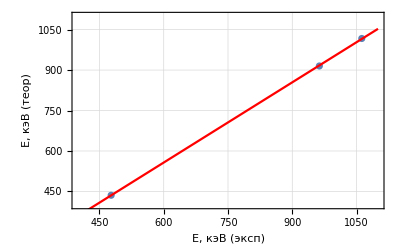

```mathematica
TableForm[Edges]
EdgesFit=LinearModelFit[QuantityMagnitude[Edges[[1;;All,2;;3]]],x,x];
Show[ListPlot[Edges[[1;;All,2;;3]],Frame->True,FrameLabel->{"E, кэВ (эксп)","E, кэВ (теор)"},PlotTheme->"Detailed",PlotRange->{{400,1100},{400,1100}}],Plot[EdgesFit["BestFit"],{x,400,1100},PlotStyle->Red]]
```

```mathematica
SinglePeak = {};
For[i=1,i≤ 9,i++,
SinglePeak=Append[SinglePeak,Import[StringJoin["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/single_peaks_csv/single_peaks_csv_0",ToString[i],".csv"]][[3;;All]]];
SinglePeak=Delete[SinglePeak,{i,1}];
]
For[i=10,i≤ 32,i++,
SinglePeak=Append[SinglePeak,Import[StringJoin["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/single_peaks_csv/single_peaks_csv_",ToString[i],".csv"]][[3;;All]]];
SinglePeak=Delete[SinglePeak,{i,1}];
]
```

```mathematica
aImpulses={ListLinePlot[SinglePeak[[1]],PlotRange-> {{-11,200},{0,2}},PlotStyle->Hue[1/43],PlotTheme->"Detailed" ] };
For[i=2,i≤ 32, i++,
aImpulses=Append[a,ListLinePlot[SinglePeak[[i]],PlotRange-> {{-11,200},{0,2}},PlotStyle-> Hue[i/43]]];
]
```

Append::normal: Nonatomic expression expected at position 1 in Append[a,].

General::stop: Further output of Append::normal will be suppressed during this calculation.

Show::gtype: Append is not a type of graphics.

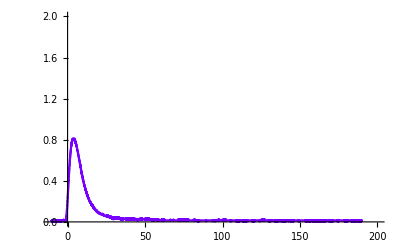
Show[Append[a,-Graphics-],PlotRange→{{-11,200},{0,1}},Frame→True,FrameLabel→{мкс,В}]

```mathematica
Show[aImpulses,PlotRange-> {{-11,200},{0,1}},Frame->True,FrameLabel->{"мкс","В"}]
```

{const→2.70297,RC→6.24354,t0→3.60658}

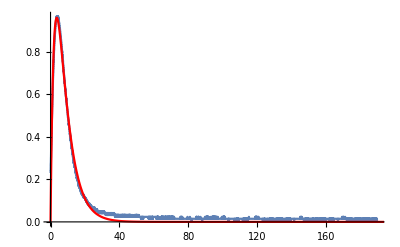

```mathematica
tauApprox=SinglePeak[[9]][[515;;All]];
ImpulseFit=FindFit[tauApprox,const*E^(-t/RC)(1-E^(-t/t0)),{const,RC,t0},t]
Show[ListLinePlot[tauApprox,PlotRange->Full],Plot[const*E^(-t/RC)(1-E^(-t/t0))/.ImpulseFit,{t,0,200},PlotRange->Full,PlotStyle->Red]]
```

```mathematica
EreverseFunc[e_]:=e/(1+2e/(Quantity[1,"ElectronMass"]*Quantity[1,"SpeedOfLight"]^2))
```

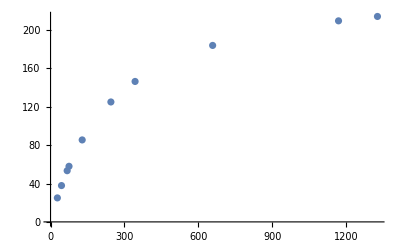

```mathematica
Ereverse=Append[{ResultTable[[2;;All,4]]},EreverseFunc[ResultTable[[2;;All,4]]]];
Ereverse=Transpose[Ereverse];
ListPlot[Ereverse]
```

```mathematica
For[i=1,i≤10,i++,
If[Ereverse[[i,1]]<UnitConvert[Quantity[1,"ElectronMass"]*Quantity[1,"SpeedOfLight"]^2,"Kiloelectronvolts"],
Ereverse[[i]]=0;
]
]
For[i=1,i≤Length[Ereverse],i++,
If[Ereverse[[i]]==0,
Ereverse=Delete[Ereverse,i];
i=1;
]
]
```

```mathematica
QuantityMagnitude[Ereverse]
```

{{1169.01,209.673},{1327.06,214.25},{658.017,184.039}}

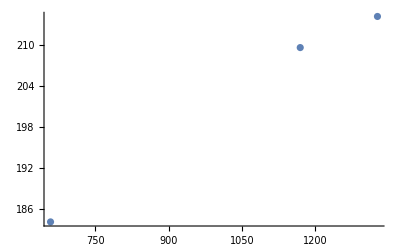

```mathematica
ListPlot[Ereverse]
```

{m→12.9503,c→6.28159}

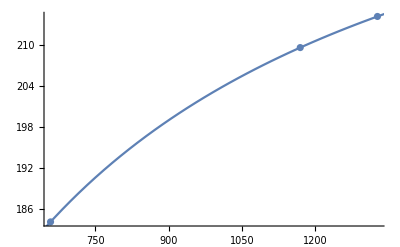

```mathematica
EreverseFit=FindFit[QuantityMagnitude[Ereverse],e/(1+2e/(m*c^2)),{m,c},e]
Show[ListPlot[Ereverse],Plot[e/(1+2e/(m*c^2))/.EreverseFit,{e,511,1350}]]
```

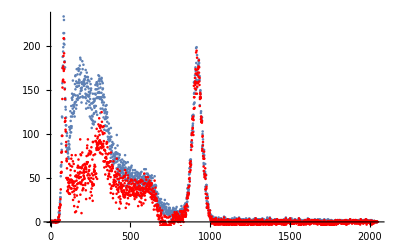

```mathematica
background=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab555/Нехаев 08-11-2018/background.xlsx"][[1]][[7;;All]];
Cleared=Transpose[{Cesium137S[[1;;All,1]]}].({{1, 0}})+Transpose[{Cesium137S[[1;;All,2]]-background[[All,2]]}].({{0, 1}});
Show[ListPlot[Cesium137S],ListPlot[Cleared,PlotStyle->Red]]
```

```mathematica
TeXForm[Grid[Ereverse]]
```

\begin{array}{cc}
 1169.01\text{keV} & 209.673\text{keV} \\
 1327.06\text{keV} & 214.25\text{keV} \\
 658.017\text{keV} & 184.039\text{keV} \\
\end{array}

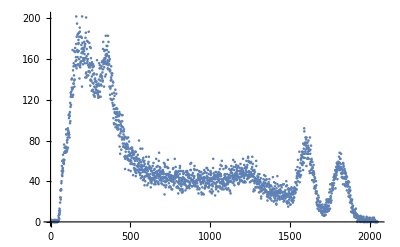

```mathematica
ListPlot[Cobalt60S]
```

```mathematica
fitReverseCo=FindFit[Cobalt60[[300;;400]],{GaussianModel[x],200≤ x0≤250 } ,{a, x0, sigma, b, c},x]
```

{a→55.9204,x0→236.749,sigma→-21.6638,b→-0.427673,c→208.158}

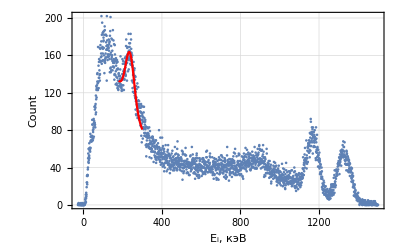

```mathematica
Show[ListPlot[Cobalt60,PlotTheme->"Detailed",Frame->True,FrameLabel->{"E_i, кэВ","Count" }],Plot[GaussianModel[x]/.fitReverseCo,{x,180,300},PlotStyle->Red]]
```

```mathematica
fitReverseCs=FindFit[Cesium137[[160;;400]],{GaussianModel[x],160≤ x0≤250 } ,{a, x0, sigma, b, c},x]
```

{a→40.0038,x0→208.282,sigma→18.356,b→-0.510467,c→216.228}

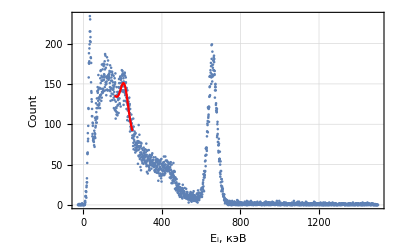

```mathematica
Show[ListPlot[Cesium137,PlotTheme->"Detailed",Frame->True,FrameLabel->{"E_i, кэВ","Count" },PlotRange->Full],Plot[GaussianModel[x]/.fitReverseCs,{x,160,250},PlotStyle->Red]]
```

{{1169.01 keV,209.673 keV},{1327.06 keV,214.25 keV},{658.017 keV,184.039 keV}}

{{1169.01 keV,236.749 keV},{1327.06 keV,236.749 keV},{658.017 keV,208.282 keV}}

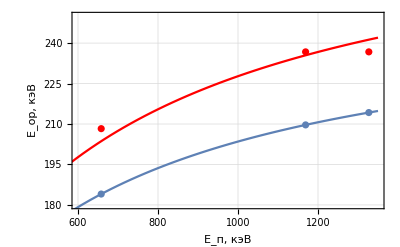

```mathematica
EreverseExperimental=Ereverse;
EreverseExperimental[[1,2]]=Quantity[x0/.fitReverseCo,"Kiloelectronvolts"];
EreverseExperimental[[2,2]]=Quantity[x0/.fitReverseCo,"Kiloelectronvolts"];
EreverseExperimental[[3,2]]=Quantity[x0/.fitReverseCs,"Kiloelectronvolts"];
EreverseExperimentalFit=FindFit[QuantityMagnitude[EreverseExperimental],e/(1+2e/(m*c^2)),{m,c},e];
Ereverse
EreverseExperimental
Show[ListPlot[Ereverse,PlotRange->{{600,1350},{180,250}},PlotTheme->"Detailed",Frame->True,FrameLabel->{"E_(:043f), кэВ","E_(:043e:0440), кэВ"}],ListPlot[EreverseExperimental,PlotRange->Full,PlotStyle->Red],Plot[e/(1+2e/(m*c^2))/.EreverseFit,{e,511,1350}],Plot[e/(1+2e/(m*c^2))/.EreverseExperimentalFit,{e,511,1350},PlotStyle->Red]]
```

{a→66.7076,x0→100.942,sigma→-29.8334,b→0.422071,c→2.59721}

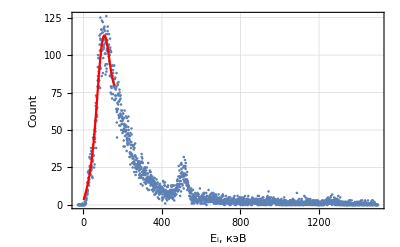

```mathematica
backgrounds=background;
For[i=1,i≤Length[backgrounds],i++,
backgrounds[[i,1]]=Calibrate[backgrounds[[i,1]]]/1000;
]
backgroundFit=FindFit[backgrounds[[1;;250]],{GaussianModel[x],90≤ x0≤ 110},{a, x0, sigma, b, c},x]
Show[ListPlot[backgrounds,PlotRange->Full,PlotTheme->"Detailed",Frame->True,FrameLabel->{"E_i, кэВ","Count" }],Plot[GaussianModel[x]/.backgroundFit,{x,1,160},PlotStyle->Red]]
```

```mathematica
x0/.backgroundFit
```

100.942